## Lecture 5: exercise

Q1: Write the expression f(x)= x e^-x + x (1 - x), and evaluate it at the points x=0, 0.1, 0.2, 0.4, 0.8.

```mathematica
f[x_] := x*Exp[-x]+x(1-x)
```

```mathematica
f[0]
f[0.1]
For[i=0, 2^i/10 < 1, i++, Print[f[2^i/10]] ] (* Overkilling :) *)
```

0

0.180484

9/100+1/(10 ⅇ^(1/10))

4/25+1/(5 ⅇ^(1/5))

6/25+2/(5 ⅇ^(2/5))

4/25+4/(5 ⅇ^(4/5))

Q2: Find the first three roots of the Bessel function J_1(x). Hint: The Bessel function in Mathematica is BesselJ[n, x]. It may also be useful to plot the function.

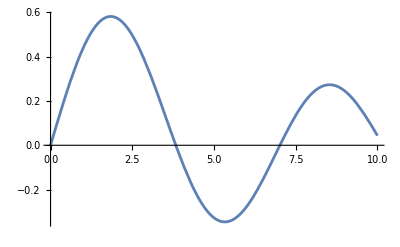

```mathematica
Plot[BesselJ[1,x], {x,0,10}]
```

```mathematica
FindRoot[BesselJ[1,x]==0,{x,0}]
FindRoot[BesselJ[1,x]==0,{x,3.9}]
FindRoot[BesselJ[1,x]==0,{x,7.}]
```

{x→0.}

{x→3.83171}

{x→7.01559}

Q3: Integrate the expression f(x) = sin(x) e^-x, and then take it’s derivative.

```mathematica
f[x_] = Sin[x]Exp[-x]
Integrate[f[x], x]
D[Integrate[f[x], x],x]
Simplify[D[Integrate[f[x], x],x]]
```

ⅇ^-x Sin[x]

-1/2 ⅇ^-x (Cos[x]+Sin[x])

-1/2 ⅇ^-x (Cos[x]-Sin[x])+1/2 ⅇ^-x (Cos[x]+Sin[x])

ⅇ^-x Sin[x]